# Notebook 01: The Graphics Command

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Introducing the Graphics command

### Circle and Disk

Here is how you use the Graphics command to draw a circle. You have to put the empty square brackets after the Circle command.



```mathematica
Graphics[Circle[]]
```

A Disk is a filled circle. Here is how you draw one. You have to put the empty square brackets after the Disk command.



```mathematica
Graphics[Disk[]]
```

### Line weights, colours and styles

Multiple drawing commands are enclosed in curly braces. A collection of items in curly braces is called a List.

Thick makes a wider line. Note that you have to change line thickness before you draw the circle.

```mathematica
Graphics[{Thick,Circle[]}]
```

-Graphics-

This is how you change the line colour and style of the circle.

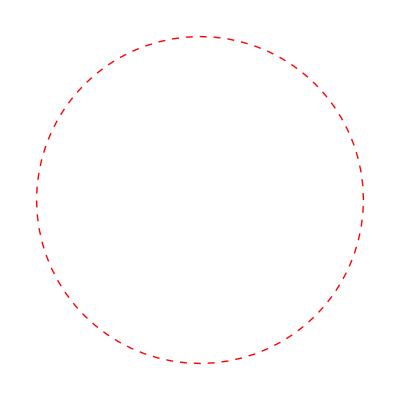

```mathematica
Graphics[{Red,Dashed, Circle[]}]
```

It doesn’t matter if you put Red before Dashed or vice versa, as long as both come before Circle.

## Coordinates and scale

Unless you specify otherwise, Mathematica draws a circle or disk centred at {0,0} with a radius of 1. We can display the coordinate system by giving Graphics the options Gridlines → Automatic and Frame → True.

You make the little arrows by typing Esc->Esc

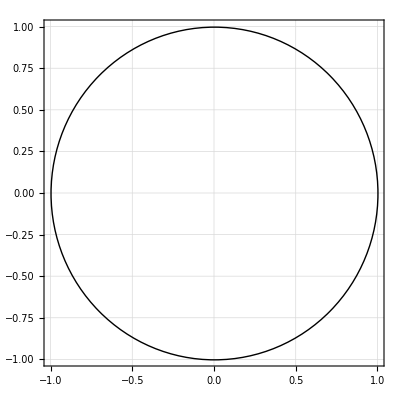

```mathematica
Graphics[{Thick,Circle[]},GridLines->Automatic,Frame->True]
```

Look at the figure above and make sure that you can identify the centre, radius and diameter of the circle.

### Moving the centre of a circle

Compare the coordinates of this circle with the previous one. We have moved it’s centre one unit to the left.

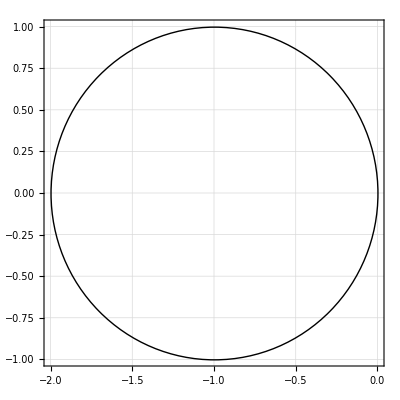

```mathematica
Graphics[{Thick,Circle[{-1,0}]},GridLines->Automatic,Frame->True]
```

### Changing the radius

Here is how you change the radius. Note the centre of this circle is the origin {0,0}

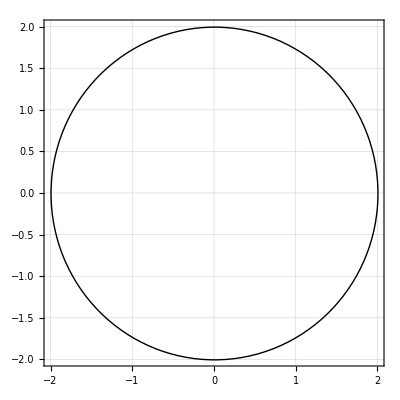

```mathematica
Graphics[{Thick,Circle[{0,0},2]},GridLines->Automatic,Frame->True]
```

### N.B. Circle size versus image size

Even though this circle has twice the radius as the one drawn before it, Mathematica renders the image of each the same size. (We can only tell they are actually different sizes by looking at their coordinates).

If we draw multiple elements in the same figure, their differences in location and size become clear.

### Changing the size of an image

We can change the size of the image (rather than the size of the object) by providing a value for the ImageSize attribute. Each of the following is a picture of the default Circle.

```mathematica
Graphics[Circle[],GridLines->Automatic,Frame->True, ImageSize->Tiny]
```

-Graphics-

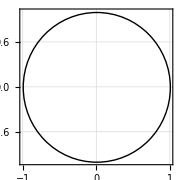

```mathematica
Graphics[Circle[],GridLines->Automatic,Frame->True, ImageSize->Small]
```

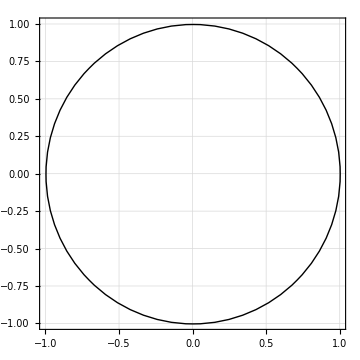

```mathematica
Graphics[Circle[],GridLines->Automatic,Frame->True, ImageSize->Medium]
```

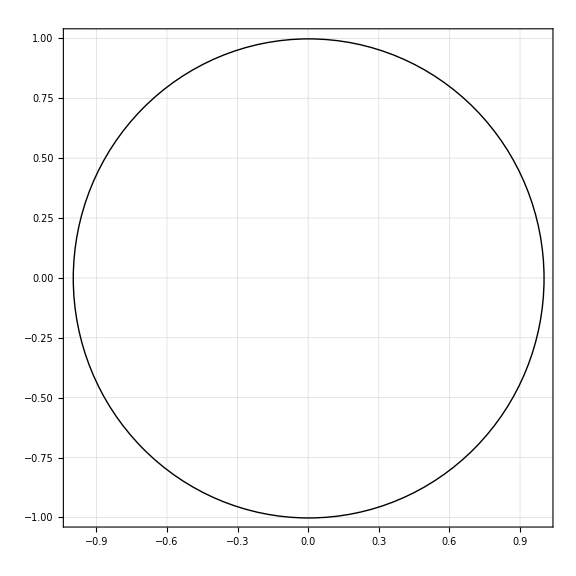

```mathematica
Graphics[Circle[],GridLines->Automatic,Frame->True, ImageSize->Large]
```

## Building up an image

### Multiple elements

Things are drawn in the order they appear in the list. Later items are drawn on top of earlier ones. Here the dotted blue circle is drawn later than--and thus on top of--the green disk.

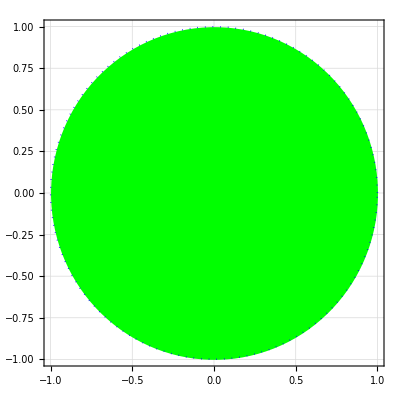

```mathematica
Graphics[{Green,Disk[],Blue, Dotted, Thick, Circle[]},GridLines->Automatic,Frame->True]
```

The green disk below is centred to the left of {0,0} by one unit. The blue circle is drawn centred on the origin. Both have a default radius of one unit.

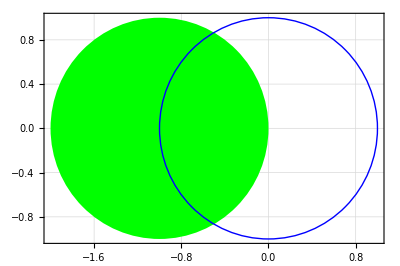

```mathematica
Graphics[{Green,Disk[{-1,0}],Blue,Circle[]},GridLines->Automatic,Frame->True]
```

Here is how you change the radius of the green disk to 1/2 unit

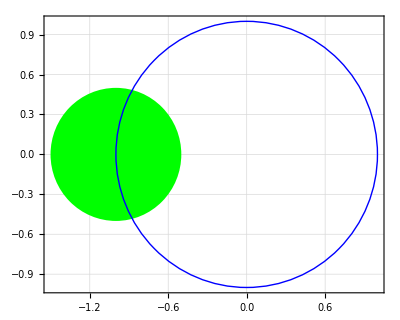

```mathematica
Graphics[{Green,Disk[{-1,0},1/2],Blue,Circle[]},GridLines->Automatic,Frame->True]
```

Here we change both radii to 1/2 unit

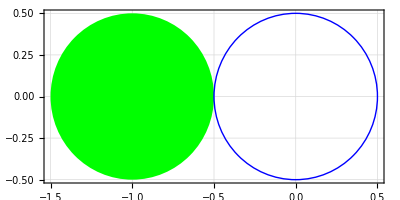

```mathematica
Graphics[{Green,Disk[{-1,0},1/2],Blue,Circle[{0,0},1/2]},GridLines->Automatic,Frame->True]
```

## Some other shapes

### Ellipse

To plot an ellipse, we use a version of the Disk command. The first pair of coordinates is the location of the centre, and the second pair is the radius in the horizontal and vertical directions.

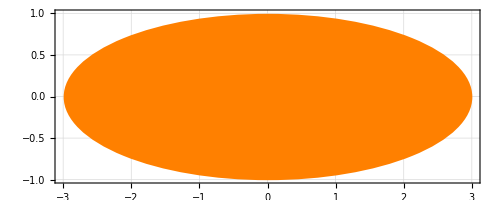

```mathematica
Graphics[{Orange,Disk[{0,0},{3,1}]},GridLines->Automatic,Frame->True]
```

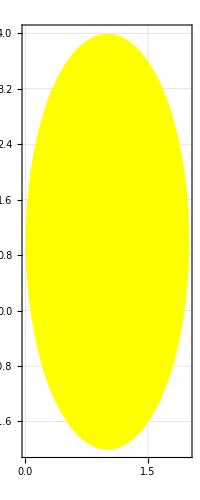

```mathematica
Graphics[{Yellow,Disk[{1,1},{1,3}]},GridLines->Automatic,Frame->True]
```

### Rectangles

The default rectangle is a filled square with the lower left corner at the origin and sides of length 1

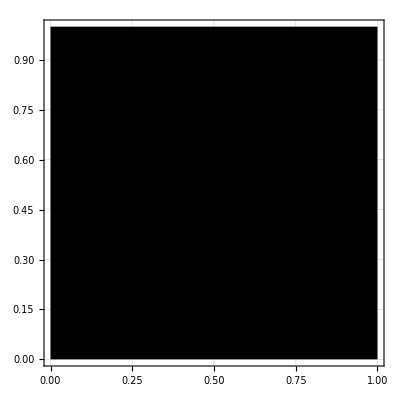

```mathematica
Graphics[Rectangle[],GridLines->Automatic,Frame->True]
```

We can move the unit square around by adjusting its lower left corner. Its sides will still have length 1

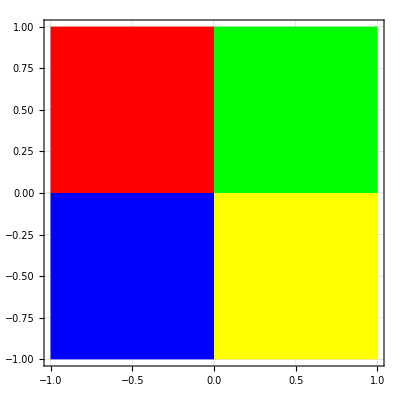

```mathematica
Graphics[{Red,Rectangle[{-1,0}],Green,Rectangle[{0,0}], Blue,Rectangle[{-1,-1}], Yellow,Rectangle[{0,-1}]},GridLines->Automatic,Frame->True]
```

If we want to draw a rectangle instead of a square, we provide coordinates for lower left and upper right hand corners.

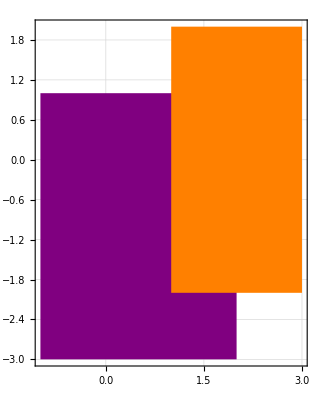

```mathematica
Graphics[{Purple,Rectangle[{-1,-3},{2,1}],Orange,Rectangle[{1,-2},{3,2}]},GridLines->Automatic,Frame->True]
```

## Symbols

We can give a collection of commands a name (in Mathematica this is called a symbol). We start with a shape we like...

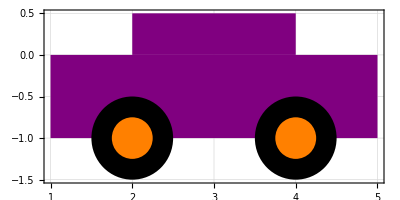

```mathematica
Graphics[{Purple,Rectangle[{1,-1},{5,0}],Rectangle[{2,0},{4,1/2}],Black,Disk[{2,-1},1/2],Disk[{4,-1},1/2],Orange,Disk[{2,-1},1/4],Disk[{4,-1},1/4]},GridLines->Automatic,Frame->True]
```

... and we pull out the list of commands and give it a name that starts with a lowercase letter. The semicolon at the end of the command suppresses any output.

```mathematica
car={Purple,Rectangle[{1,-1},{5,0}],Rectangle[{2,0},{4,1/2}],Black,Disk[{2,-1},1/2],Disk[{4,-1},1/2],Orange,Disk[{2,-1},1/4],Disk[{4,-1},1/4]};
```

Now we can draw the object with the following command.

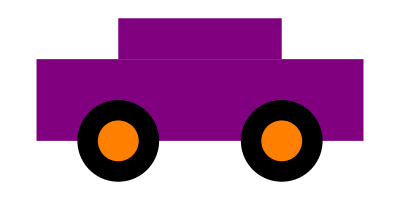

```mathematica
Graphics[car]
```

If we want to draw a background, we can include that as follows. The Join command puts the contents of multiple lists into a single list.

```mathematica
background={LightBlue,Rectangle[{0,-2},{6,1}]};
```

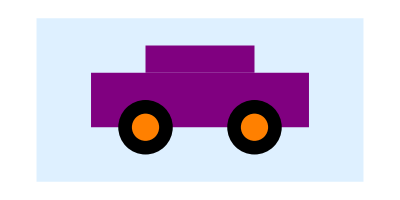

```mathematica
Graphics[Join[background,car]]
```

In this case we have used absolute coordinates for the object we are drawing. The car, in other words, will always be centred at the same point, which is {3,-1/2}. We will soon learn a better way to do things.

## In-Class Activity

### Using the Graphics command, draw a picture that has at least six elements.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course